## Derive Transcedental Equation

adjust the propagation in the air and diamond portions of the cavities to include Guoy phase and higher order TEM modes - (1) DIAMOND, (2) AIR

```mathematica
Mirror = {{1/Sqrt[1-r^2], -r/Sqrt[1-r^2]},{- r/Sqrt[1-r^2], 1/Sqrt[1-r^2]}}; 

Interface[n1_, n2_]:= ({{(n1+n2)/(2 n2), (-n1+n2)/(2 n2)}, {(-n1+n2)/(2 n2), (n1+n2)/(2 n2)}}); (* This is going from n1 into n2 *)

T1={{ⅇ^(ⅈ ((2 n1 π z1)/λ-(1+m+n) ArcTan[(z1 λ)/(n1 π w01^2)])),0},{0,ⅇ^(-ⅈ ((2 n1 π z1)/λ-(1+m+n) ArcTan[(z1 λ)/(n1 π w01^2)]))}}/.n1->nd;
T2={{ⅇ^(ⅈ ((2 n2 π (L-z1))/λ-(1+m+n) (ArcTan[((L-z02) λ)/(n2 π w02^2)]-ArcTan[((-z02+z1) λ)/(n2 π w02^2)]))),0},{0,ⅇ^(-ⅈ ((2 n2 π (L-z1))/λ-(1+m+n) (ArcTan[((L-z02) λ)/(n2 π w02^2)]-ArcTan[((-z02+z1) λ)/(n2 π w02^2)])))}}/.n2-> 1;

MStackold = (Mirror).T2.Interface[nd,1].T1.Interface[1,nd].(Inverse[Mirror]);

Transold = 1/Simplify[(ComplexExpand[((MStackold[[2,2]])*(MStackold[[2,2]]/.Complex[0, n_]-> -Complex[0,n]))/.{m->k,z1->td,L->ta+td}]),Assumptions-> { nd>0, td>0, ta>0,w01>0,w02>0,z02>0, λ>0,r>-1,r<1, {nd,td,ta,λ,r,w01,w02,z02,π}∈Reals,{k,n}∈Integers}]
```

### Old mirrors have r=-1

```mathematica
z= Simplify[Simplify[Limit[(1-r^2)^2/Transold, r-> -1]]/.Arg[1+ⅈ*a_]-> ArcTan[a]/.Arg[1-ⅈ*a_]-> -ArcTan[a]/.ta->L-td/.λ->c/ν]
```

1/nd^2((1+nd) Sin[(2 π (L-td) ν)/c+(2 nd π td ν)/c-(1+k+n) ArcTan[(c td)/(nd π w01^2 ν)]-(1+k+n) (ArcTan[(c (L-z02))/(π w02^2 ν)]-ArcTan[(c (td-z02))/(π w02^2 ν)])]+(-1+nd) Sin[(2 π (L-td) ν)/c-(2 nd π td ν)/c+(1+k+n) ArcTan[(c td)/(nd π w01^2 ν)]-(1+k+n) (ArcTan[(c (L-z02))/(π w02^2 ν)]-ArcTan[(c (td-z02))/(π w02^2 ν)])])^2

The resonance condition is met when this quantity goes to zero, therefore the quantity in the square root should also go to zero.

```mathematica
resonanceOld=Simplify[(1+nd) Sin[(2 π ta ν)/c+(2 nd π td ν)/c-(1+k+n) ArcTan[(c td)/(nd π w01^2 ν)]-(1+k+n) (ArcTan[(c (L-z02))/(π w02^2 ν)]-ArcTan[(c (td-z02))/(π w02^2 ν)])]+(-1+nd) Sin[(2 π ta ν)/c-(2 nd π td ν)/c+(1+k+n) ArcTan[(c td)/(nd π w01^2 ν)]-(1+k+n) (ArcTan[(c (L-z02))/(π w02^2 ν)]-ArcTan[(c (td-z02))/(π w02^2 ν)])]];
```

### Checking Limits with Lily’s Gaussian parameters

Check limit where td->0, using Lily’s Gaussian parameters:

```mathematica
(*lensparam=Simplify[{z02->td*(1-1/nd),w01-> Sqrt[λ/Pi]*((ta+td/nd)*(R0-(ta+td/nd)))^1/4,w02->  Sqrt[λ/Pi]*((ta+td/nd)*(R0-(ta+td/nd)))^1/4}/.λ->c/ν/.ta->(L-td)];*)

newGauss = {z02->(π^2 (n1^4 w01^4 z1-n1^2 n2^2 w01^4 z1))/(n1^4 π^2 w01^4+n2^2 z1^2 λ^2),w02->(n1 w01 (n1^2 π^2 w01^4+z1^2 λ^2))/(√(n1^6 π^4 w01^8+n1^4 π^2 w01^4 z1^2 λ^2+n1^2 n2^2 π^2 w01^4 z1^2 λ^2+n2^2 z1^4 λ^4))}/.{n1->nd,n2->1,z1->td};
waistsoln = {w01->1/(2^(1/4) √π)(1/(n1^4 n2^2)(-L^2 n1^4 λ^2-n1^4 R0 z1 λ^2+n1^2 n2^2 R0 z1 λ^2-n1^4 z1^2 λ^2+L n1^2 (-2 n2^2 z1+n1^2 (R0+2 z1)) λ^2+√(n1^4 (L^4 n1^4+z1^2 (n2^2 R0-n1^2 (R0+z1))^2-2 L^3 (-2 n1^2 n2^2 z1+n1^4 (R0+2 z1))+2 L n1^2 z1 (-n1^2 (R0^2+3 R0 z1+2 z1^2)+n2^2 (R0^2+4 R0 z1+2 z1^2))+L^2 n1^2 (-2 n2^2 z1 (3 R0+4 z1)+n1^2 (R0^2+6 R0 z1+6 z1^2))) λ^4)))^(1/4)}/.{n1->nd,n2->1,z1->td};
```

```mathematica
νtest[L_,R0_,k_]=ν/.Solve[Simplify[resonanceOld/.newGauss/.waistsoln/.{ta->L-td}/.{td->0,n->0}/.λ->c/ν,Assumptions->{{L,c,nd, ν,R0}∈Reals,L>0,c>0,nd>0, ν>0,R0>0,R0>L}]==0,ν][[1]]/.C[1]->0
```

(c (ArcTan[√(L/(-L+R0))]+k ArcTan[√(L/(-L+R0))]))/(2 L π)

Divide the two terms to make sure it gives you the correct frequency spacing...

```mathematica
Simplify[((R0/.Simplify[Solve[δν==Simplify[νtest[L,R0,1]-νtest[L,R0,0]],R0]][[1]]))/(-L/(-1+Cos[(2 L π δν)/c]^2))]
```

1

```mathematica
R0/.Simplify[Solve[δν==Simplify[νtest[L,R0,1]-νtest[L,R0,0]],R0]][[1]]
```

L Csc[(2 L π δν)/c]^2

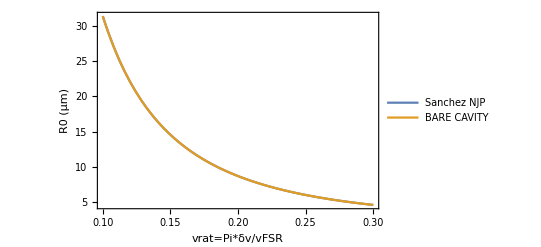

```mathematica
R0sanchez[L_,vrat_]=-L/(-1+Cos[Pi*vrat]^2);
R0bare[L_,vrat_]=L Csc[ π *vrat]^2;
Plot[{R0sanchez[3*10^-6,vrat]*10^6,R0bare[3*10^-6,vrat]*10^6},{vrat,0.1,0.3},PlotLegends->{"Sanchez NJP","BARE CAVITY"},FrameLabel-> {"vrat=Pi*δv/vFSR","R0 (μm)"},Frame->True]
```

This works for the bare cavity case! td->0

## Solving for Frequency

As Lily noted, there are terms like w02^2 ν,  w01^2 ν in the ArcTan arguements... this cancels out the frequency dependence. For example:

```mathematica
FullSimplify[((w01)^2*ν)/.waistsoln/.λ->c/ν,Assumptions->{{L,c,nd, ν,R0,td}∈Reals,L>0,c>0,nd>0, ν>0,R0>0,td>0,R0>L}]
```

1/(√2 nd π)c √(L nd^2 (-L+R0)+(-1+nd^2) (2 L-R0) td-nd^2 td^2+√(L^2 nd^4 (L-R0)^2-2 L nd^2 (-1+nd^2) (2 L^2-3 L R0+R0^2) td+(L^2 (-8 nd^2+6 nd^4)+2 L nd^2 (4-3 nd^2) R0+(-1+nd^2)^2 R0^2) td^2-2 nd^2 (-1+nd^2) (2 L-R0) td^3+nd^4 td^4))

```mathematica
resonanceOld2 = Simplify[resonanceOld/.{w02->Sqrt[ w022v/ν], w01->Sqrt[ w011v/ν]}/.ta->L-td]
```

(1+nd) Sin[(2 π (L-td) ν)/c+(2 nd π td ν)/c-(1+k+n) ArcTan[(c td)/(nd π w011v)]-(1+k+n) (ArcTan[(c (L-z02))/(π w022v)]-ArcTan[(c (td-z02))/(π w022v)])]+(-1+nd) Sin[(2 π (L-td) ν)/c-(2 nd π td ν)/c+(1+k+n) ArcTan[(c td)/(nd π w011v)]-(1+k+n) (ArcTan[(c (L-z02))/(π w022v)]-ArcTan[(c (td-z02))/(π w022v)])]

Set the first term to zero to get the resonances condition? This is eqivalent to the estimate we do with the 1D model:

```mathematica
vbase = ν/.Simplify[Solve[(2 π (L-td) ν)/c+(2 nd π td ν)/c-(1+k+n) ArcTan[(c td)/(nd π w011v)]-(1+k+n) (ArcTan[(c (L-z02))/(π w022v)]-ArcTan[(c (td-z02))/(π w022v)])==m*Pi, ν]][[1]]
```

(c (m π+(1+k+n) ArcTan[(c td)/(nd π w011v)]+(1+k+n) (ArcTan[(c (L-z02))/(π w022v)]-ArcTan[(c (td-z02))/(π w022v)])))/(2 π (L+(-1+nd) td))

This is the same as the 1D solution with some additional contributions from the Guoy phase. Substitute vbase and a small deviation into resonanceOld2

```mathematica
Simplify[resonanceOld2/.ν->vbase+δν]
```

(1+nd) Sin[(π (c m+2 (L+(-1+nd) td) δν))/c]+(-1+nd) Sin[1/(c (L+(-1+nd) td))(c L m π-c m π td-c m nd π td+2 L^2 π δν-4 L π td δν+2 π td^2 δν-2 nd^2 π td^2 δν+2 c (1+k+n) (L-td) ArcTan[(c td)/(nd π w011v)]-2 c (1+k+n) nd td ArcTan[(c (L-z02))/(π w022v)]+2 c nd td ArcTan[(c (td-z02))/(π w022v)]+2 c k nd td ArcTan[(c (td-z02))/(π w022v)]+2 c n nd td ArcTan[(c (td-z02))/(π w022v)])]

Now where to throw out terms of δv....divide first term by second:

```mathematica
Simplify[(π (c m+2 (L+(-1+nd) td) δν))/c/.L->ta+td]/Simplify[Simplify[1/(c (L+(-1+nd) td))(c L m π-c m π td-c m nd π td+2 L^2 π δν-4 L π td δν+2 π td^2 δν-2 nd^2 π td^2 δν)]/.L->ta+td]
```

(ta+nd td)/(ta-nd td)

OK the first term is bigger, neglect the stuff in the second term. We should also pull the factor of m out of the first Sin[] term -> sin(a+b)=cos(b) sin(a) + cos(a) sin(b))

```mathematica
deltav = Simplify[Solve[(1+nd)*(-1)^m* Sin[(π (2 (L+(-1+nd) td) δν))/c]+(-1+nd) Sin[1/(c (L+(-1+nd) td))(c L m π-c m π td-c m nd π td+2 c (1+k+n) (L-td) ArcTan[(c td)/(nd π w011v)]-2 c (1+k+n) nd td ArcTan[(c (L-z02))/(π w022v)]+2 c nd td ArcTan[(c (td-z02))/(π w022v)]+2 c k nd td ArcTan[(c (td-z02))/(π w022v)]+2 c n nd td ArcTan[(c (td-z02))/(π w022v)])]==0,δν]]
```

{{δν→ConditionalExpression[-1/(2 π (L+(-1+nd) td))c (ArcSin[1/(1+nd)(-1)^-m (-1+nd) Sin[1/(L+(-1+nd) td)(L m π-m π td-m nd π td+2 (1+k+n) (L-td) ArcTan[(c td)/(nd π w011v)]-2 (1+k+n) nd td ArcTan[(c (L-z02))/(π w022v)]+2 nd td ArcTan[(c (td-z02))/(π w022v)]+2 k nd td ArcTan[(c (td-z02))/(π w022v)]+2 n nd td ArcTan[(c (td-z02))/(π w022v)])]]-2 π C[1]),C[1]∈Integers]},{δν→ConditionalExpression[1/(2 π (L+(-1+nd) td))c (π+ArcSin[1/(1+nd)(-1)^-m (-1+nd) Sin[1/(L+(-1+nd) td)(L m π-m π td-m nd π td+2 (1+k+n) (L-td) ArcTan[(c td)/(nd π w011v)]-2 (1+k+n) nd td ArcTan[(c (L-z02))/(π w022v)]+2 nd td ArcTan[(c (td-z02))/(π w022v)]+2 k nd td ArcTan[(c (td-z02))/(π w022v)]+2 n nd td ArcTan[(c (td-z02))/(π w022v)])]]+2 π C[1]),C[1]∈Integers]}}

```mathematica
vsolve1 =Simplify[vbase+δν/.(deltav[[1]]/.C[1]->0)]
vsolve2 = Simplify[vbase+δν/.(deltav[[2]]/.C[1]->0)];
```

1/(2 π (L+(-1+nd) td))c (m π-ArcSin[1/(1+nd)(-1)^-m (-1+nd) Sin[1/(L+(-1+nd) td)(L m π-m π td-m nd π td+2 (1+k+n) (L-td) ArcTan[(c td)/(nd π w011v)]-2 (1+k+n) nd td ArcTan[(c (L-z02))/(π w022v)]+2 nd td ArcTan[(c (td-z02))/(π w022v)]+2 k nd td ArcTan[(c (td-z02))/(π w022v)]+2 n nd td ArcTan[(c (td-z02))/(π w022v)])]]+(1+k+n) ArcTan[(c td)/(nd π w011v)]+(1+k+n) (ArcTan[(c (L-z02))/(π w022v)]-ArcTan[(c (td-z02))/(π w022v)]))

We now have the new resonance condition (pull (-1)^m out of ArcSin)... this has some strong similarities to the 1D case!

```mathematica
resonanceOld3 = 1/(2 π (L+(-1+nd) td))c (m π-(-1)^m*ArcSin[1/(1+nd) (-1+nd) Sin[1/(L+(-1+nd) td)(L m π-m π td-m nd π td+2 (1+k+n) (L-td) ArcTan[(c td)/(nd π w011v)]-2 (1+k+n) nd td ArcTan[(c (L-z02))/(π w022v)]+2 nd td ArcTan[(c (td-z02))/(π w022v)]+2 k nd td ArcTan[(c (td-z02))/(π w022v)]+2 n nd td ArcTan[(c (td-z02))/(π w022v)])]]+(1+k+n) ArcTan[(c td)/(nd π w011v)]+(1+k+n) (ArcTan[(c (L-z02))/(π w022v)]-ArcTan[(c (td-z02))/(π w022v)]));
```

Now we need to replace the cavity parameters, and let’s assume we only look at one transverse mode number k (n=0)

```mathematica
resonanceOld4[td_,L_,m_,R0_,k_] = Simplify[resonanceOld3/.{w022v->w02^2*ν,w011v->w01^2*ν}/.newGauss/.waistsoln/.n->0/.λ->c/ν,Assumptions->{{L,c,nd, ν,R0,td}∈Reals,L>0,c>0,nd>0, ν>0,R0>0,td>0,R0>L}]
```

1/(2 π (L+(-1+nd) td))c (m π+(-1)^(1+m) ArcSin[1/(1+nd)(-1+nd) Sin[1/(L+(-1+nd) td)(L m π-m π td-m nd π td+2 (1+k) (L-td) ArcTan[(√2 td)/(√(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]+2 (1+k) nd td ArcTan[(√2 td)/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]-2 nd td ArcTan[(√2 (-L^3 nd^4+L^2 (-3 nd^2 td+nd^4 (R0+3 td))+(-1+nd^2) td ((-1+nd^2) R0 td+nd^2 td^2-√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))+L nd^2 (-2 (-1+nd^2) R0 td+4 td^2-3 nd^2 td^2+√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))))/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))) (-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td+2 td^2-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]-2 k nd td ArcTan[(√2 (-L^3 nd^4+L^2 (-3 nd^2 td+nd^4 (R0+3 td))+(-1+nd^2) td ((-1+nd^2) R0 td+nd^2 td^2-√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))+L nd^2 (-2 (-1+nd^2) R0 td+4 td^2-3 nd^2 td^2+√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))))/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))) (-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td+2 td^2-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))])]]+(1+k) ArcTan[(√2 td)/(√(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]-ArcTan[(√2 td)/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]-k ArcTan[(√2 td)/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]+ArcTan[(√2 (-L^3 nd^4+L^2 (-3 nd^2 td+nd^4 (R0+3 td))+(-1+nd^2) td ((-1+nd^2) R0 td+nd^2 td^2-√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))+L nd^2 (-2 (-1+nd^2) R0 td+4 td^2-3 nd^2 td^2+√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))))/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))) (-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td+2 td^2-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))]+k ArcTan[(√2 (-L^3 nd^4+L^2 (-3 nd^2 td+nd^4 (R0+3 td))+(-1+nd^2) td ((-1+nd^2) R0 td+nd^2 td^2-√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))+L nd^2 (-2 (-1+nd^2) R0 td+4 td^2-3 nd^2 td^2+√(L^4 nd^4+td^2 ((-1+nd^2) R0+nd^2 td)^2+2 L nd^2 td (-(-1+nd^2) R0^2+(4-3 nd^2) R0 td-2 (-1+nd^2) td^2)-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2))))))/(nd √(-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))) (-L^2 nd^2+L nd^2 R0-2 L td+2 L nd^2 td+R0 td-nd^2 R0 td+2 td^2-nd^2 td^2+√(L^4 nd^4+td^2 (R0-nd^2 (R0+td))^2-2 L^3 (-2 nd^2 td+nd^4 (R0+2 td))+2 L nd^2 td (R0^2+4 R0 td+2 td^2-nd^2 (R0^2+3 R0 td+2 td^2))+L^2 nd^2 (-2 td (3 R0+4 td)+nd^2 (R0^2+6 R0 td+6 td^2)))))])

Plot this and the transcedental equation:

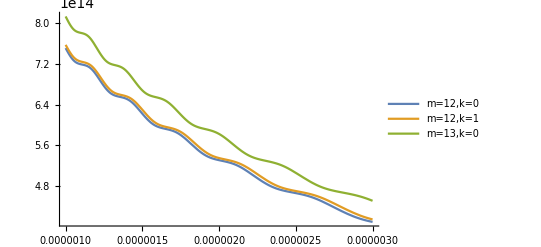

```mathematica
Plot[{resonanceOld4[10^-6,L,12,10^-5,0]/.{nd->2.417,c->3*10^8},resonanceOld4[10^-6,L,12,10^-5,1]/.{nd->2.417,c->3*10^8},resonanceOld4[10^-6,L,13,10^-5,0]/.{nd->2.417,c->3*10^8}},{L,10^-6,3*10^-6},PlotLegends->{"m=12,k=0","m=12,k=1","m=13,k=0"}]
```

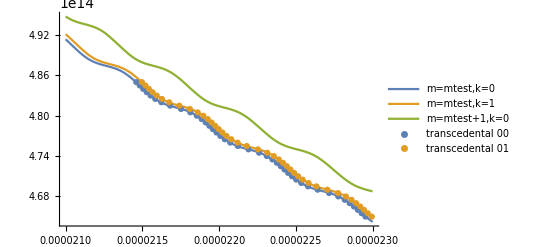

```mathematica
resonanceOldtrans[td_,L_,R0_,k_,ν_]=resonanceOld/.newGauss/.waistsoln/.n->0/.λ->c/ν/.ta->L-td;

tdtest= 10*10^-6;
Rtest = 10^-4;
mtest=115;

Lmin=21*10^-6;
Lmax = 23*10^-6;
vdiv=0.5*10^12;
fmin = 465*10^12;
fmax = 485*10^12;

vtrans = N[Table[ν,{ν,fmin,fmax,vdiv}]];

Lcurr00 = Lmax;
Lcurr01 = Lmax;

solntrans00= {};
solntrans01= {};

Do[
Lnew00 = L/.FindRoot[(resonanceOldtrans[tdtest,L,Rtest,0,v]/.{nd->2.417,c->3*10^8})==0,{L,Lcurr00}];
Lnew01= L/.FindRoot[(resonanceOldtrans[tdtest,L,Rtest,1,v]/.{nd->2.417,c->3*10^8})==0,{L,Lcurr01}];

Lcurr00=Lnew00;
Lcurr01=Lnew01;
solntrans00=Append[solntrans00,{Lcurr00,v}];
solntrans01=Append[solntrans01,{Lcurr01,v}],
{v,Min[vtrans],Max[vtrans],vdiv}];

trans1=ListPlot[{solntrans00,solntrans01},PlotLegends->{"transcedental 00", "transcedental 01"}];
num1 = Plot[{resonanceOld4[tdtest,L,mtest,Rtest,0]/.{nd->2.417,c->3*10^8},resonanceOld4[tdtest,L,mtest,Rtest,1]/.{nd->2.417,c->3*10^8},resonanceOld4[tdtest,L,mtest+1,Rtest,0]/.{nd->2.417,c->3*10^8}},{L,Lmin,Lmax},PlotLegends->{"m=mtest,k=0","m=mtest,k=1","m=mtest+1,k=0"}];

Show[num1,trans1]
```

## Use Suzanne’s Expressions and redo...

```mathematica
lensparam=Simplify[{z02->td*(1-1/nd),w01-> Sqrt[λ/Pi]*((ta+td/nd)*(R0-(ta+td/nd)))^(1/4),w02->  Sqrt[λ/Pi]*((ta+td/nd)*(R0-(ta+td/nd)))^(1/4)}/.λ->c/ν/.ta->(L-td)];

resonance5[td_,L_,m_,R0_,k_] = Simplify[resonanceOld3/.{w022v->w02^2*ν,w011v->w01^2*ν}/.lensparam/.n->0]
```

(c (m π+(-1)^(1+m) ArcSin[1/(1+nd)(-1+nd) Sin[(L m π-m π td-m nd π td+2 (1+k) (L-td) ArcTan[td/(nd √((L+(-1+1/nd) td) (-L+R0+td-td/nd)))]-2 (1+k) nd td ArcTan[(L+(-1+1/nd) td)/(√((L+(-1+1/nd) td) (-L+R0+td-td/nd)))]+2 nd td ArcTan[td/(nd √(-((L nd+td-nd td) (L nd+td-nd (R0+td)))/nd^2))]+2 k nd td ArcTan[td/(nd √(-((L nd+td-nd td) (L nd+td-nd (R0+td)))/nd^2))])/(L+(-1+nd) td)]]+(1+k) ArcTan[(L nd+td-nd td)/(nd √(-((L nd+td-nd td) (L nd+td-nd (R0+td)))/nd^2))]))/(2 π (L+(-1+nd) td))

Plotting

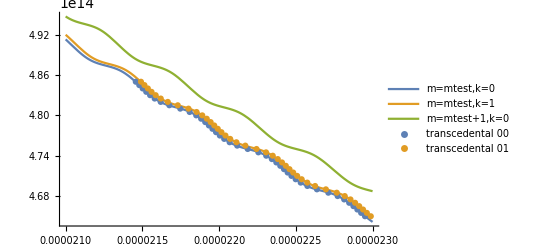

```mathematica
resonanceOldtrans2[td_,L_,R0_,k_,ν_]=resonanceOld/.lensparam/.n->0/.λ->c/ν/.ta->(L-td)/.n->0;

tdtest= 10*10^-6;
Rtest = 10^-4;
mtest=115;

Lmin=21*10^-6;
Lmax = 23*10^-6;
vdiv=0.5*10^12;
fmin = 465*10^12;
fmax = 485*10^12;

vtrans = N[Table[ν,{ν,fmin,fmax,vdiv}]];

Lcurr00 = Lmax;
Lcurr01 = Lmax;

solntrans00= {};
solntrans01= {};

Do[
Lnew00 = L/.FindRoot[(resonanceOldtrans2[tdtest,L,Rtest,0,v]/.{nd->2.417,c->3*10^8})==0,{L,Lcurr00}];
Lnew01= L/.FindRoot[(resonanceOldtrans2[tdtest,L,Rtest,1,v]/.{nd->2.417,c->3*10^8})==0,{L,Lcurr01}];

Lcurr00=Lnew00;
Lcurr01=Lnew01;
solntrans00=Append[solntrans00,{Lcurr00,v}];
solntrans01=Append[solntrans01,{Lcurr01,v}],
{v,Min[vtrans],Max[vtrans],vdiv}];

trans1=ListPlot[{solntrans00,solntrans01},PlotLegends->{"transcedental 00", "transcedental 01"}];
num1 = Plot[{resonance5[tdtest,L,mtest,Rtest,0]/.{nd->2.417,c->3*10^8},resonance5[tdtest,L,mtest,Rtest,1]/.{nd->2.417,c->3*10^8},resonance5[tdtest,L,mtest+1,Rtest,0]/.{nd->2.417,c->3*10^8}},{L,Lmin,Lmax},PlotLegends->{"m=mtest,k=0","m=mtest,k=1","m=mtest+1,k=0"}];

Show[num1,trans1]
```

```mathematica
Simplify[resonance5[td,L,m,R0,k],Assumptions->{R0>0,td>0,nd>0,L>0,R0>L,R0>td}]
```

1/(2 π (L+(-1+nd) td))c (m π+(-1)^(1+m) ArcSin[1/(1+nd)(-1+nd) Sin[1/(L+(-1+nd) td)(m π (L-(1+nd) td)+2 (1+k) (L+(-1+nd) td) ArcTan[td/(√(-(L nd+td-nd td) (L nd+td-nd (R0+td))))]-2 (1+k) nd td ArcTan[(L nd+td-nd td)/(√(-(L nd+td-nd td) (L nd+td-nd (R0+td))))])]]+(1+k) ArcTan[(L nd+td-nd td)/(√(-(L nd+td-nd td) (L nd+td-nd (R0+td))))])

I think the key would be to fit this expression simultaneously for a few resonances...double-check limits:

```mathematica
Limit[resonance5[td,L,m,R0,k],R0->Infinity]
```

(c (m π+(-1)^(1+m) ArcSin[((-1+nd) Sin[(m π (L-(1+nd) td))/(L+(-1+nd) td)])/(1+nd)]))/(2 π (L+(-1+nd) td))

This gives the right result :)